```mathematica
f[t_,i0_,j0_,n_]:=Module[{i,j},
Table[
Table[
If[(i==i0&&j==i0)||(i==j0&&j==j0),Cos[t],
If[(i==i0&&j==j0),-Sin[t],
If[(i==j0&&j==i0),Sin[t],
If[i==j,1,0]]]],
{j,1,n}],
{i,1,n}]]
```

```mathematica
r12[t12_]:=f[t12,1,2,2]
```

```mathematica
r12[t1]//MatrixForm
```

(Cos[t1] | -Sin[t1]
Sin[t1] | Cos[t1])

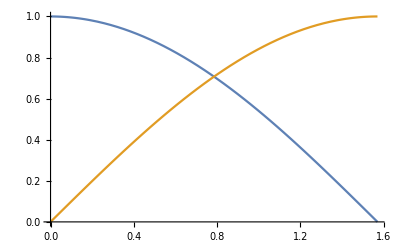

```mathematica
Plot[{Cos[t1],Sin[t1]},{t1,0,Pi/2}]
```

```mathematica
r12[Pi/4]//MatrixForm
```

(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))

```mathematica
r13[t12_,t13_]:=f[t12,1,2,3].f[t13,1,3,3]
```

```mathematica
r13[t1,t2]//MatrixForm
```

(Cos[t1] Cos[t2] | -Sin[t1] | -Cos[t1] Sin[t2]
Cos[t2] Sin[t1] | Cos[t1] | -Sin[t1] Sin[t2]
Sin[t2] | 0 | Cos[t2])

```mathematica
r13[ArcTan[1/Sqrt[1]],t2]//MatrixForm
```

(Cos[t2]/(√2) | -1/(√2) | -Sin[t2]/(√2)
Cos[t2]/(√2) | 1/(√2) | -Sin[t2]/(√2)
Sin[t2] | 0 | Cos[t2])

```mathematica
r13[ArcTan[1/Sqrt[1]],ArcTan[1/Sqrt[2]]]//MatrixForm
```

(1/(√3) | -1/(√2) | -1/(√6)
1/(√3) | 1/(√2) | -1/(√6)
1/(√3) | 0 | √(2/3))

```mathematica
r14[t12_,t13_,t14_]:=f[t12,1,2,4].f[t13,1,3,4].f[t14,1,4,4]
```

```mathematica
r14[t1,t2,t3]//MatrixForm
```

(Cos[t1] Cos[t2] Cos[t3] | -Sin[t1] | -Cos[t1] Sin[t2] | -Cos[t1] Cos[t2] Sin[t3]
Cos[t2] Cos[t3] Sin[t1] | Cos[t1] | -Sin[t1] Sin[t2] | -Cos[t2] Sin[t1] Sin[t3]
Cos[t3] Sin[t2] | 0 | Cos[t2] | -Sin[t2] Sin[t3]
Sin[t3] | 0 | 0 | Cos[t3])

```mathematica
r14[ArcTan[1/Sqrt[1]],ArcTan[1/Sqrt[2]],ArcTan[1/Sqrt[3]]]//MatrixForm
```

(1/2 | -1/(√2) | -1/(√6) | -1/(2 √3)
1/2 | 1/(√2) | -1/(√6) | -1/(2 √3)
1/2 | 0 | √(2/3) | -1/(2 √3)
1/2 | 0 | 0 | (√3)/2)

```mathematica
r15[t12_,t13_,t14_,t15_]:=f[t12,1,2,5].f[t13,1,3,5].f[t14,1,4,5].f[t15,1,5,5]
```

```mathematica
r15[t1,t2,t3,t4]//MatrixForm
```

(Cos[t1] Cos[t2] Cos[t3] Cos[t4] | -Sin[t1] | -Cos[t1] Sin[t2] | -Cos[t1] Cos[t2] Sin[t3] | -Cos[t1] Cos[t2] Cos[t3] Sin[t4]
Cos[t2] Cos[t3] Cos[t4] Sin[t1] | Cos[t1] | -Sin[t1] Sin[t2] | -Cos[t2] Sin[t1] Sin[t3] | -Cos[t2] Cos[t3] Sin[t1] Sin[t4]
Cos[t3] Cos[t4] Sin[t2] | 0 | Cos[t2] | -Sin[t2] Sin[t3] | -Cos[t3] Sin[t2] Sin[t4]
Cos[t4] Sin[t3] | 0 | 0 | Cos[t3] | -Sin[t3] Sin[t4]
Sin[t4] | 0 | 0 | 0 | Cos[t4])

```mathematica
r15[ArcTan[1/Sqrt[1]],ArcTan[1/Sqrt[2]],ArcTan[1/Sqrt[3]],ArcTan[1/Sqrt[4]]]//MatrixForm
```

(1/(√5) | -1/(√2) | -1/(√6) | -1/(2 √3) | -1/(2 √5)
1/(√5) | 1/(√2) | -1/(√6) | -1/(2 √3) | -1/(2 √5)
1/(√5) | 0 | √(2/3) | -1/(2 √3) | -1/(2 √5)
1/(√5) | 0 | 0 | (√3)/2 | -1/(2 √5)
1/(√5) | 0 | 0 | 0 | 2/(√5))

```mathematica
r16[t12_,t13_,t14_,t15_,t16_]:=f[t12,1,2,6].f[t13,1,3,6].f[t14,1,4,6].f[t15,1,5,6].f[t16,1,6,6]
```

```mathematica
r16[t1,t2,t3,t4,t5]//MatrixForm
```

(Cos[t1] Cos[t2] Cos[t3] Cos[t4] Cos[t5] | -Sin[t1] | -Cos[t1] Sin[t2] | -Cos[t1] Cos[t2] Sin[t3] | -Cos[t1] Cos[t2] Cos[t3] Sin[t4] | -Cos[t1] Cos[t2] Cos[t3] Cos[t4] Sin[t5]
Cos[t2] Cos[t3] Cos[t4] Cos[t5] Sin[t1] | Cos[t1] | -Sin[t1] Sin[t2] | -Cos[t2] Sin[t1] Sin[t3] | -Cos[t2] Cos[t3] Sin[t1] Sin[t4] | -Cos[t2] Cos[t3] Cos[t4] Sin[t1] Sin[t5]
Cos[t3] Cos[t4] Cos[t5] Sin[t2] | 0 | Cos[t2] | -Sin[t2] Sin[t3] | -Cos[t3] Sin[t2] Sin[t4] | -Cos[t3] Cos[t4] Sin[t2] Sin[t5]
Cos[t4] Cos[t5] Sin[t3] | 0 | 0 | Cos[t3] | -Sin[t3] Sin[t4] | -Cos[t4] Sin[t3] Sin[t5]
Cos[t5] Sin[t4] | 0 | 0 | 0 | Cos[t4] | -Sin[t4] Sin[t5]
Sin[t5] | 0 | 0 | 0 | 0 | Cos[t5])

```mathematica
r16[ArcTan[1/Sqrt[1]],ArcTan[1/Sqrt[2]],ArcTan[1/Sqrt[3]],ArcTan[1/Sqrt[4]],ArcTan[1/Sqrt[5]]]//MatrixForm
```

(1/(√6) | -1/(√2) | -1/(√6) | -1/(2 √3) | -1/(2 √5) | -1/(√30)
1/(√6) | 1/(√2) | -1/(√6) | -1/(2 √3) | -1/(2 √5) | -1/(√30)
1/(√6) | 0 | √(2/3) | -1/(2 √3) | -1/(2 √5) | -1/(√30)
1/(√6) | 0 | 0 | (√3)/2 | -1/(2 √5) | -1/(√30)
1/(√6) | 0 | 0 | 0 | 2/(√5) | -1/(√30)
1/(√6) | 0 | 0 | 0 | 0 | √(5/6))

```mathematica
r17[t12_,t13_,t14_,t15_,t16_,t17_]:=f[t12,1,2,7].f[t13,1,3,7].f[t14,1,4,7].f[t15,1,5,7].f[t16,1,6,7].f[t17,1,7,7]
```

```mathematica
r17[t1,t2,t3,t4,t5,t6]//MatrixForm
```

(Cos[t1] Cos[t2] Cos[t3] Cos[t4] Cos[t5] Cos[t6] | -Sin[t1] | -Cos[t1] Sin[t2] | -Cos[t1] Cos[t2] Sin[t3] | -Cos[t1] Cos[t2] Cos[t3] Sin[t4] | -Cos[t1] Cos[t2] Cos[t3] Cos[t4] Sin[t5] | -Cos[t1] Cos[t2] Cos[t3] Cos[t4] Cos[t5] Sin[t6]
Cos[t2] Cos[t3] Cos[t4] Cos[t5] Cos[t6] Sin[t1] | Cos[t1] | -Sin[t1] Sin[t2] | -Cos[t2] Sin[t1] Sin[t3] | -Cos[t2] Cos[t3] Sin[t1] Sin[t4] | -Cos[t2] Cos[t3] Cos[t4] Sin[t1] Sin[t5] | -Cos[t2] Cos[t3] Cos[t4] Cos[t5] Sin[t1] Sin[t6]
Cos[t3] Cos[t4] Cos[t5] Cos[t6] Sin[t2] | 0 | Cos[t2] | -Sin[t2] Sin[t3] | -Cos[t3] Sin[t2] Sin[t4] | -Cos[t3] Cos[t4] Sin[t2] Sin[t5] | -Cos[t3] Cos[t4] Cos[t5] Sin[t2] Sin[t6]
Cos[t4] Cos[t5] Cos[t6] Sin[t3] | 0 | 0 | Cos[t3] | -Sin[t3] Sin[t4] | -Cos[t4] Sin[t3] Sin[t5] | -Cos[t4] Cos[t5] Sin[t3] Sin[t6]
Cos[t5] Cos[t6] Sin[t4] | 0 | 0 | 0 | Cos[t4] | -Sin[t4] Sin[t5] | -Cos[t5] Sin[t4] Sin[t6]
Cos[t6] Sin[t5] | 0 | 0 | 0 | 0 | Cos[t5] | -Sin[t5] Sin[t6]
Sin[t6] | 0 | 0 | 0 | 0 | 0 | Cos[t6])

```mathematica
r17[ArcTan[1/Sqrt[1]],ArcTan[1/Sqrt[2]],ArcTan[1/Sqrt[3]],ArcTan[1/Sqrt[4]],ArcTan[1/Sqrt[5]],ArcTan[1/Sqrt[6]]]//MatrixForm
```

(1/(√7) | -1/(√2) | -1/(√6) | -1/(2 √3) | -1/(2 √5) | -1/(√30) | -1/(√42)
1/(√7) | 1/(√2) | -1/(√6) | -1/(2 √3) | -1/(2 √5) | -1/(√30) | -1/(√42)
1/(√7) | 0 | √(2/3) | -1/(2 √3) | -1/(2 √5) | -1/(√30) | -1/(√42)
1/(√7) | 0 | 0 | (√3)/2 | -1/(2 √5) | -1/(√30) | -1/(√42)
1/(√7) | 0 | 0 | 0 | 2/(√5) | -1/(√30) | -1/(√42)
1/(√7) | 0 | 0 | 0 | 0 | √(5/6) | -1/(√42)
1/(√7) | 0 | 0 | 0 | 0 | 0 | √(6/7))

```mathematica
r18[t12_,t13_,t14_,t15_,t16_,t17_,t18_]:=f[t12,1,2,8].f[t13,1,3,8].f[t14,1,4,8].f[t15,1,5,8].f[t16,1,6,8].f[t17,1,7,8].f[t18,1,8,8]
```

```mathematica
r18[t1,t2,t3,t4,t5,t6,t7]//MatrixForm
```

(Cos[t1] Cos[t2] Cos[t3] Cos[t4] Cos[t5] Cos[t6] Cos[t7] | -Sin[t1] | -Cos[t1] Sin[t2] | -Cos[t1] Cos[t2] Sin[t3] | -Cos[t1] Cos[t2] Cos[t3] Sin[t4] | -Cos[t1] Cos[t2] Cos[t3] Cos[t4] Sin[t5] | -Cos[t1] Cos[t2] Cos[t3] Cos[t4] Cos[t5] Sin[t6] | -Cos[t1] Cos[t2] Cos[t3] Cos[t4] Cos[t5] Cos[t6] Sin[t7]
Cos[t2] Cos[t3] Cos[t4] Cos[t5] Cos[t6] Cos[t7] Sin[t1] | Cos[t1] | -Sin[t1] Sin[t2] | -Cos[t2] Sin[t1] Sin[t3] | -Cos[t2] Cos[t3] Sin[t1] Sin[t4] | -Cos[t2] Cos[t3] Cos[t4] Sin[t1] Sin[t5] | -Cos[t2] Cos[t3] Cos[t4] Cos[t5] Sin[t1] Sin[t6] | -Cos[t2] Cos[t3] Cos[t4] Cos[t5] Cos[t6] Sin[t1] Sin[t7]
Cos[t3] Cos[t4] Cos[t5] Cos[t6] Cos[t7] Sin[t2] | 0 | Cos[t2] | -Sin[t2] Sin[t3] | -Cos[t3] Sin[t2] Sin[t4] | -Cos[t3] Cos[t4] Sin[t2] Sin[t5] | -Cos[t3] Cos[t4] Cos[t5] Sin[t2] Sin[t6] | -Cos[t3] Cos[t4] Cos[t5] Cos[t6] Sin[t2] Sin[t7]
Cos[t4] Cos[t5] Cos[t6] Cos[t7] Sin[t3] | 0 | 0 | Cos[t3] | -Sin[t3] Sin[t4] | -Cos[t4] Sin[t3] Sin[t5] | -Cos[t4] Cos[t5] Sin[t3] Sin[t6] | -Cos[t4] Cos[t5] Cos[t6] Sin[t3] Sin[t7]
Cos[t5] Cos[t6] Cos[t7] Sin[t4] | 0 | 0 | 0 | Cos[t4] | -Sin[t4] Sin[t5] | -Cos[t5] Sin[t4] Sin[t6] | -Cos[t5] Cos[t6] Sin[t4] Sin[t7]
Cos[t6] Cos[t7] Sin[t5] | 0 | 0 | 0 | 0 | Cos[t5] | -Sin[t5] Sin[t6] | -Cos[t6] Sin[t5] Sin[t7]
Cos[t7] Sin[t6] | 0 | 0 | 0 | 0 | 0 | Cos[t6] | -Sin[t6] Sin[t7]
Sin[t7] | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t7])

```mathematica
r18[ArcTan[1/Sqrt[1]],ArcTan[1/Sqrt[2]],ArcTan[1/Sqrt[3]],ArcTan[1/Sqrt[4]],ArcTan[1/Sqrt[5]],ArcTan[1/Sqrt[6]],ArcTan[1/Sqrt[7]]]//MatrixForm
```

(1/(2 √2) | -1/(√2) | -1/(√6) | -1/(2 √3) | -1/(2 √5) | -1/(√30) | -1/(√42) | -1/(2 √14)
1/(2 √2) | 1/(√2) | -1/(√6) | -1/(2 √3) | -1/(2 √5) | -1/(√30) | -1/(√42) | -1/(2 √14)
1/(2 √2) | 0 | √(2/3) | -1/(2 √3) | -1/(2 √5) | -1/(√30) | -1/(√42) | -1/(2 √14)
1/(2 √2) | 0 | 0 | (√3)/2 | -1/(2 √5) | -1/(√30) | -1/(√42) | -1/(2 √14)
1/(2 √2) | 0 | 0 | 0 | 2/(√5) | -1/(√30) | -1/(√42) | -1/(2 √14)
1/(2 √2) | 0 | 0 | 0 | 0 | √(5/6) | -1/(√42) | -1/(2 √14)
1/(2 √2) | 0 | 0 | 0 | 0 | 0 | √(6/7) | -1/(2 √14)
1/(2 √2) | 0 | 0 | 0 | 0 | 0 | 0 | (√(7/2))/2)